```mathematica
Integrate[√(((1-t)(a1x-a2x)+t(b1x-b2x))^2+((1-t)(a1y-a2y)+t(b1y-b2y))^2),{t,0,1}]
```

$Aborted

```mathematica
(* numerical definition of distance*)
```

```mathematica
SegmentDist[{a1_?(VectorQ[#,NumericQ]&),b1_?(VectorQ[#,NumericQ]&)},{a2_?(VectorQ[#,NumericQ]&),b2_?(VectorQ[#,NumericQ]&)}]:=NIntegrate[Norm[(1-t)(a1-a2)+t(b1-b2)],{t,0,1}]
```

```mathematica
SegmentDist[{{1,1},{0,1}},{{0,0},{1,0}}]
```

1.14779

```mathematica
(* derivation of closed form expression *)
```

```mathematica
Expand[((1-t)(a1x-a2x)+t(b1x-b2x))^2+((1-t)(a1y-a2y)+t(b1y-b2y))^2]
```

a1x^2+a1y^2-2 a1x a2x+a2x^2-2 a1y a2y+a2y^2-2 a1x^2 t-2 a1y^2 t+4 a1x a2x t-2 a2x^2 t+4 a1y a2y t-2 a2y^2 t+2 a1x b1x t-2 a2x b1x t+2 a1y b1y t-2 a2y b1y t-2 a1x b2x t+2 a2x b2x t-2 a1y b2y t+2 a2y b2y t+a1x^2 t^2+a1y^2 t^2-2 a1x a2x t^2+a2x^2 t^2-2 a1y a2y t^2+a2y^2 t^2-2 a1x b1x t^2+2 a2x b1x t^2+b1x^2 t^2-2 a1y b1y t^2+2 a2y b1y t^2+b1y^2 t^2+2 a1x b2x t^2-2 a2x b2x t^2-2 b1x b2x t^2+b2x^2 t^2+2 a1y b2y t^2-2 a2y b2y t^2-2 b1y b2y t^2+b2y^2 t^2

```mathematica
Collect[%,t]
```

a1x^2+a1y^2-2 a1x a2x+a2x^2-2 a1y a2y+a2y^2+(-2 a1x^2-2 a1y^2+4 a1x a2x-2 a2x^2+4 a1y a2y-2 a2y^2+2 a1x b1x-2 a2x b1x+2 a1y b1y-2 a2y b1y-2 a1x b2x+2 a2x b2x-2 a1y b2y+2 a2y b2y) t+(a1x^2+a1y^2-2 a1x a2x+a2x^2-2 a1y a2y+a2y^2-2 a1x b1x+2 a2x b1x+b1x^2-2 a1y b1y+2 a2y b1y+b1y^2+2 a1x b2x-2 a2x b2x-2 b1x b2x+b2x^2+2 a1y b2y-2 a2y b2y-2 b1y b2y+b2y^2) t^2

```mathematica
(* use result from integral table *)
```

```mathematica
const[{a1x_,a1y_},{a2x_,a2y_}]:=a1x^2+a1y^2-2 a1x a2x+a2x^2-2 a1y a2y+a2y^2;
lin[{a1x_,a1y_},{a2x_,a2y_},{b1x_,b1y_},{b2x_,b2y_}]:=(-2 a1x^2-2 a1y^2+4 a1x a2x-2 a2x^2+4 a1y a2y-2 a2y^2+2 a1x b1x-2 a2x b1x+2 a1y b1y-2 a2y b1y-2 a1x b2x+2 a2x b2x-2 a1y b2y+2 a2y b2y) 
quad[{a1x_,a1y_},{a2x_,a2y_},{b1x_,b1y_},{b2x_,b2y_}]:=(a1x^2+a1y^2-2 a1x a2x+a2x^2-2 a1y a2y+a2y^2-2 a1x b1x+2 a2x b1x+b1x^2-2 a1y b1y+2 a2y b1y+b1y^2+2 a1x b2x-2 a2x b2x-2 b1x b2x+b2x^2+2 a1y b2y-2 a2y b2y-2 b1y b2y+b2y^2)
SegmentDist2[{a1_?(VectorQ[#,NumericQ]&),b1_?(VectorQ[#,NumericQ]&)},{a2_?(VectorQ[#,NumericQ]&),b2_?(VectorQ[#,NumericQ]&)}]:=Module[{c=const[a1,a2],b=lin[a1,a2,b1,b2],a=quad[a1,a2,b1,b2]},
(b+2a)/(4a)√(a+b+c)-b/(4a)√c+(4a c-b^2)/(8 a^(3/2))Log[Abs[(2a+b+2 √(a(a+b+c)))/(b+2 √(a c))]]
]
```

```mathematica
a1={1,0};
b1={2,0};
a2={2,0};
b2={3,0};
const[a1,a2]
lin[a1,a2,b1,b2]
quad[a1,a2,b1,b2]
Timing[SegmentDist[{a1,b1},{a2,b2}]]
Timing[SegmentDist2[{a1,b1},{a2,b2}]]
Clear[a1,a2,b1,b2]
```

1

0

0

{0.00284,1.}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{0.007471,Indeterminate}

```mathematica
(* closed form is much faster *)
```

```mathematica
Timing[SegmentDist[{{1,1},{0,1}},{{2.5,.1},{3.5,.1}}]]
```

{0.014047,2.66483}

```mathematica
Timing[SegmentDist2[{{1,1},{0,1}},{{2.5,.1},{3.5,.1}}]]
```

{0.000255,2.66483}

```mathematica
(* triangle inequality *)
```

```mathematica
SegmentDist[{{1,0},{0,0}},{{0,0},{0,1}}]
SegmentDist[{{1,0},{0,0}},{{0,0},{(√2)/2,(√2)/2}}]
SegmentDist[{{0,0},{(√2)/2,(√2)/2}},{{0,0},{0,1}}]
```

0.811613

0.62799

0.382683

```mathematica
(* visualize Subscript[s, α], discretizing here is overkill as it's always a line segment *)
```

```mathematica
segmentaslist[a_,b_,n_]:=Table[(1-t)a+t b,{t,0,1,1/n}]
averagesegments[seg1_,seg2_,alpha_]:=(1-alpha)seg1+alpha seg2
```

```mathematica
s1=segmentaslist[{0,0},{0,1},100];
s2=segmentaslist[{.5,.1},{.5,.1}+{Cos[.3],Sin[.3]},100];
```

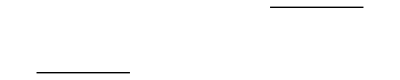

```mathematica
Graphics[{Line[s1],Line[s2]}]
```

```mathematica
Manipulate[as=averagesegments[s1,s2,f];
{Graphics[{Line[s1],Line[s2],Red,Line[as]},AspectRatio->Automatic],Norm[as[[1]]-as[[Length[as]]]]},{f,0,1},TrackedSymbols->True]
```

```mathematica
(* objective function - distance+constraint to have equally spaced points *)
```

```mathematica
fff[a0_?(VectorQ[#,NumericQ]&),b0_?(VectorQ[#,NumericQ]&),a1_?(VectorQ[#,NumericQ]&),b1_?(VectorQ[#,NumericQ]&),ax_?(VectorQ[#,NumericQ]&),ay_?(VectorQ[#,NumericQ]&),bx_?(VectorQ[#,NumericQ]&),by_?(VectorQ[#,NumericQ]&),n_?NumericQ]:=Module[{p0,p1,p2,p3},
p0=SegmentDist2[{a0,b0},{{ax[[1]],ay[[1]]},{bx[[1]],by[[1]]}}];
p1=SegmentDist2[{a1,b1},{{ax[[n-2]],ay[[n-2]]},{bx[[n-2]],by[[n-2]]}}];
p2=Table[SegmentDist2[{{ax[[i]],ay[[i]]},{bx[[i]],by[[i]]}},{{ax[[i+1]],ay[[i+1]]},{bx[[i+1]],by[[i+1]]}}],{i,n-3}];
p3=Join[{p0},p2,{p1}];
Total[p3]+100000Sum[(p3[[i]]-p3[[i+1]])^2,{i,n-2}]]
```

```mathematica
FindChain[{a0_,b0_},{a1_,b1_},n_]:=Module[{s,test,head,tail,mid,diff,minres,temp},
test=Table[head=(1-a)a0+a a1;
tail=(1-a)b0+a b1;
mid=(head+tail)/2;
diff=head-mid;
diff=diff/(2*Norm[diff]);
{mid+diff,mid-diff}
,{a,0,1,1/n}];
minres=FindMinimum[{
f=fff[a0,b0,a1,b1,Table[ax[i],{i,n-2}],Table[ay[i],{i,n-2}],Table[bx[i],{i,n-2}],Table[by[i],{i,n-2}],n]
,
Table[Norm[{ax[i]-bx[i],ay[i]-by[i]}]==1,{i,n-2}]},
Join[Table[{ax[i],test[[i+1,1,1]]},{i,n-2}],
Table[{ay[i],test[[i+1,1,2]]},{i,n-2}],Table[{bx[i],test[[i+1,2,1]]},{i,n-2}],Table[{by[i],test[[i+1,2,2]]},{i,n-2}]](*,EvaluationMonitor:>Print[{f,{ax[1],ay[1]},Norm[{ax[1]-bx[1],ay[1]-by[1]}],{bx[1],by[1]}}]*)];
temp=Table[{{ax[i],ay[i]},{bx[i],by[i]}}/.minres[[2]],{i,n-2}];
Join[{{a0,b0}},temp,{{a1,b1}}]
]
```

```mathematica
Timing[test3=FindChain[{{0,0},{1,0}},{{1,0},{1,1}},3]]
```

{0.088986,{{{0,0},{1,0}},{{0.329568,0.0225597},{1.16611,0.570465}},{{1,0},{1,1}}}}

```mathematica
Timing[test4=FindChain[{{0,0},{1,0}},{{1,0},{1,1}},4]]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.67624×10^-6, 0.000964551, 0}, is returned.

{17.1038,{{{0,0},{1,0}},{{0.261523,-0.0202285},{1.21656,0.276272}},{{0.541346,-0.0469792},{1.18858,0.715312}},{{1,0},{1,1}}}}

```mathematica
Timing[test5=FindChain[{{0,0},{1,0}},{{1,0},{1,1}},5]]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {2.44072×10^-7, 0.00147346, 0}, is returned.

{38.0388,{{{0,0},{1,0}},{{0.152776,0.0250422},{1.1243,0.261965}},{{0.373528,-0.0489926},{1.16526,0.561873}},{{0.635403,-0.0468955},{1.1112,0.832661}},{{1,0},{1,1}}}}

```mathematica
Timing[test6=FindChain[{{0,0},{1,0}},{{1,0},{1,1}},6]]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.03662×10^-6, 0.0109857, 0}, is returned.

{74.6221,{{{0,0},{1,0}},{{0.0618794,0.089691},{1.05017,0.242303}},{{0.265244,-0.0658997},{1.14782,0.404271}},{{0.454807,-0.0760057},{1.13205,0.659759}},{{0.693923,-0.0552118},{1.08518,0.865071}},{{1,0},{1,1}}}}

```mathematica
Timing[test7=FindChain[{{0,0},{1,0}},{{1,0},{1,1}},7]]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.38877×10^-7, 0.059378, 0}, is returned.

{130.497,{{{0,0},{1,0}},{{0.0559426,0.0674139},{1.04753,0.196822}},{{0.210881,-0.0415752},{1.13266,0.346143}},{{0.361383,-0.0694055},{1.14058,0.55738}},{{0.545504,-0.0809151},{1.10597,0.747262}},{{0.749598,-0.0511165},{1.06797,0.89685}},{{1,0},{1,1}}}}

```mathematica
Timing[test8=FindChain[{{0,0},{1,0}},{{1,0},{1,1}},8]]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.64773×10^-6, 0.0451042, 0}, is returned.

{206.632,{{{0,0},{1,0}},{{0.0373465,0.0661028},{1.03132,0.175746}},{{0.171421,-0.059586},{1.117,0.26582}},{{0.264389,-0.0488451},{1.12161,0.466112}},{{0.426519,-0.08778},{1.1185,0.634141}},{{0.599478,-0.0861773},{1.08926,0.785672}},{{0.783223,-0.0520339},{1.05424,0.91054}},{{1,0},{1,1}}}}

```mathematica
Timing[test9=FindChain[{{0,0},{1,0}},{{1,0},{1,1}},9]]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {3.38583×10^-7, 0.0133135, 0}, is returned.

{313.139,{{{0,0},{1,0}},{{0.0368369,0.0544349},{1.03202,0.152479}},{{0.150851,-0.0492937},{1.11058,0.23164}},{{0.219077,-0.0357851},{1.11367,0.411099}},{{0.358934,-0.0872954},{1.12885,0.550851}},{{0.49577,-0.095152},{1.10223,0.699961}},{{0.650852,-0.0838048},{1.07299,0.822725}},{{0.812167,-0.0479953},{1.04537,0.924433}},{{1,0},{1,1}}}}

```mathematica
Timing[test10=FindChain[{{0,0},{1,0}},{{1,0},{1,1}},10]]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {5.63469×10^-7, 0.0156114, 0}, is returned.

{435.095,{{{0,0},{1,0}},{{0.0391834,0.0445677},{1.03544,0.13098}},{{0.137321,-0.0421022},{1.10489,0.210501}},{{0.188771,-0.0225595},{1.11016,0.366094}},{{0.306114,-0.0745598},{1.13123,0.490402}},{{0.42074,-0.0910656},{1.11541,0.628266}},{{0.552298,-0.0952054},{1.09034,0.747715}},{{0.691232,-0.0785745},{1.06414,0.849295}},{{0.835517,-0.0442641},{1.03865,0.934888}},{{1,0},{1,1}}}}

```mathematica
SegmentDist2[{{0,0},{1,0}},{{1,0},{1,1}}]
```

1/2+Log[(2+2 √2)/(-2+2 √2)]/(4 √2)

```mathematica
N[%]
```

0.811613

```mathematica
Table[SegmentDist2[test3[[i]],test3[[i+1]]],{i,2}]
Sum[SegmentDist2[test3[[i]],test3[[i+1]]],{i,2}]
```

{0.411564,0.411566}

0.82313

```mathematica
Table[SegmentDist2[test4[[i]],test4[[i+1]]],{i,3}]
Sum[SegmentDist2[test4[[i]],test4[[i+1]]],{i,3}]
```

{0.283176,0.283179,0.283183}

0.849538

```mathematica
Table[SegmentDist2[test5[[i]],test5[[i+1]]],{i,4}]
Sum[SegmentDist2[test5[[i]],test5[[i+1]]],{i,4}]
```

{0.206937,0.206948,0.206965,0.206977}

0.827826

```mathematica
Table[SegmentDist2[test6[[i]],test6[[i+1]]],{i,5}]
Sum[SegmentDist2[test6[[i]],test6[[i+1]]],{i,5}]
```

{0.176136,0.176125,0.176129,0.176138,0.176148}

0.880676

```mathematica
Table[SegmentDist2[test7[[i]],test7[[i+1]]],{i,6}]
Sum[SegmentDist2[test7[[i]],test7[[i+1]]],{i,6}]
```

{0.142871,0.14291,0.142874,0.142863,0.142865,0.142869}

0.857251

```mathematica
Table[SegmentDist2[test8[[i]],test8[[i+1]]],{i,7}]
Sum[SegmentDist2[test8[[i]],test8[[i+1]]],{i,7}]
```

{0.126174,0.126179,0.126199,0.126239,0.126275,0.126254,0.126249}

0.883568

```mathematica
Table[SegmentDist2[test9[[i]],test9[[i+1]]],{i,8}]
Sum[SegmentDist2[test9[[i]],test9[[i+1]]],{i,8}]
```

{0.109572,0.109569,0.109561,0.109549,0.109546,0.10955,0.109559,0.109567}

0.876473

```mathematica
Table[SegmentDist2[test10[[i]],test10[[i+1]]],{i,9}]
Sum[SegmentDist2[test10[[i]],test10[[i+1]]],{i,9}]
```

{0.0960444,0.0960518,0.0960592,0.0960861,0.0961199,0.0961568,0.0961932,0.0962235,0.0962414}

0.865176

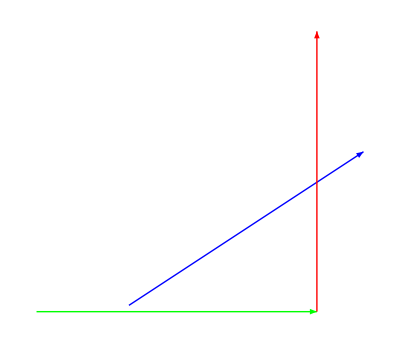

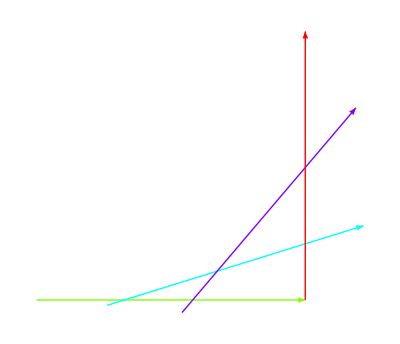

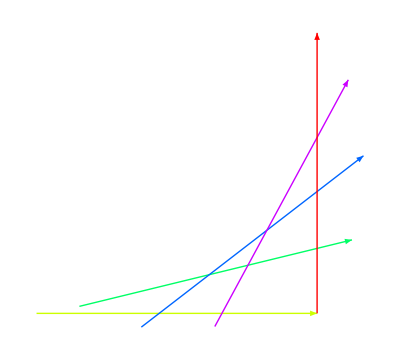

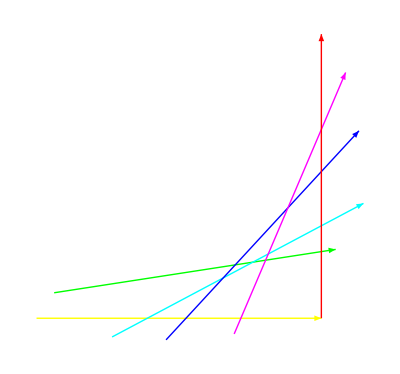

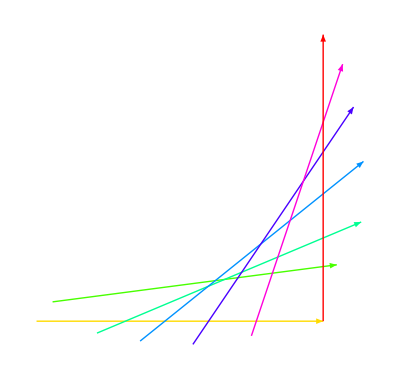

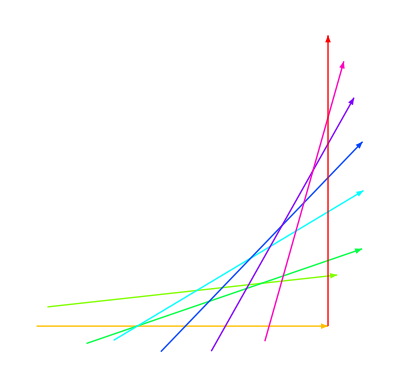

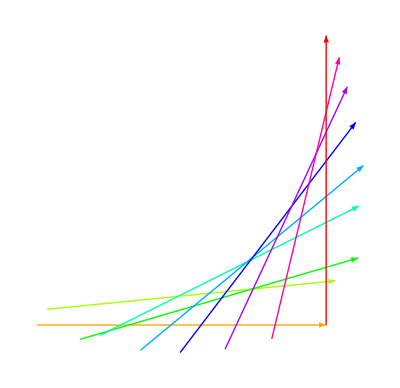

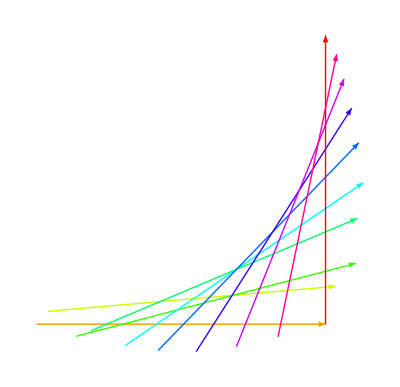

```mathematica
Graphics[Table[{Hue[i/Length[test3]],Arrow[test3[[i]]]},{i,Length[test3]}]]
Graphics[Table[{Hue[i/Length[test4]],Arrow[test4[[i]]]},{i,Length[test4]}]]
Graphics[Table[{Hue[i/Length[test5]],Arrow[test5[[i]]]},{i,Length[test5]}]]
Graphics[Table[{Hue[i/Length[test6]],Arrow[test6[[i]]]},{i,Length[test6]}]]
Graphics[Table[{Hue[i/Length[test7]],Arrow[test7[[i]]]},{i,Length[test7]}]]
Graphics[Table[{Hue[i/Length[test8]],Arrow[test8[[i]]]},{i,Length[test8]}]]
Graphics[Table[{Hue[i/Length[test9]],Arrow[test9[[i]]]},{i,Length[test9]}]]
Graphics[Table[{Hue[i/Length[test10]],Arrow[test10[[i]]]},{i,Length[test10]}]]
```

```mathematica
a1={1,0};b1={2,0};a2={-1,0};b2={-1+Cos[π+.001],Sin[π+.001]};
Timing[anti3=FindChain[{a1,b1},{a2,b2},10]]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {3.52785×10^-6, 0.000667825, 0}, is returned.

{456.097,{{{1,0},{2,0}},{{0.632749,-0.0097388},{1.63275,-0.0102351}},{{0.265401,-0.00708224},{1.2654,-0.00803159}},{{-0.101791,-0.0103474},{0.898163,-0.0200196}},{{-0.446351,0.134482},{0.523076,-0.110913}},{{-0.0842448,0.435324},{-0.214702,-0.55613}},{{0.0821243,0.128952},{-0.892097,-0.0966421}},{{-0.266157,0.00198792},{-1.26612,-0.00636875}},{{-0.63307,0.00295909},{-1.63307,0.00433803}},{{-1,0},{-2.,-0.001}}}}

```mathematica
SegmentDist2[{a1,b1},{a2,b2}]-3
```

-2.01713×10^-7

```mathematica
b2[[1]]+2
```

5.×10^-7

```mathematica
Table[SegmentDist2[anti3[[i]],anti3[[i+1]]],{i,9}]
Sum[SegmentDist2[anti3[[i]],anti3[[i+1]]],{i,9}]
```

{0.367387,0.367356,0.367302,0.367238,0.367168,0.367099,0.367037,0.366986,0.366955}

3.30453

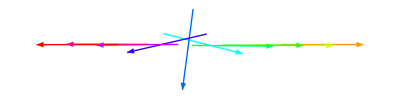

```mathematica
Graphics[Table[{Hue[i/Length[anti3]],Arrow[anti3[[i]]]},{i,Length[anti3]}]]
```

```mathematica
(* broken, dividing by zero *)
a1={1,0};
b1={2,0};
a2={-1,0};
b2={-2,0};
Timing[anti3=FindChain[{a1,b1},{a2,b2},3]]
```

$Aborted